# Just launch the code below to run the notebook (shift+enter)

```mathematica
ClearAll["Global`*"]
BlockEvaluation[tag_]:=Block[{},
nb=EvaluationNotebook[];
NotebookFind[nb,tag,All,CellTags];
SelectionEvaluate[nb]
]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Auxiliary data"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Auxiliary data"}]]];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Auxiliary data/ALPs with gluon coupling"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Auxiliary data/ALPs with gluon coupling"}]]];
tagslist={"Evaluation","Evaluation-sensitivity"};
choiceslist={"Tabulated number of events+sensitivity","Sensitivity only"};
computationchoice=dropdownDialog[choiceslist,"Do you want to compute the tabulated number of events and then sensitivity, or just sensitivity (if the tabulate number of events has been already produced)?"];
tagselected=If[computationchoice=="Tabulated number of events+sensitivity","Evaluation","Evaluation-sensitivity"];
BlockEvaluation[tagselected]
```

# Preliminary definitions

## Parameters and various functions

```mathematica
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
infoDialog[phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],Button["Proceed",DialogReturn[choice]]}]]
(*chbar*)
chbar= 6.6*10^-25*3*10^8;
(*Decay width of mesons*)
τπ0=8.52*10^-17;
Γπ0=chbar/τπ0;
τB=1.64*10^-12;
hbar=6.58*10^-25;
ΓBdecayGeV=hbar/τB;
(*Bare quark masses from pdg*)
md=4.67*10^-3;
mu=2.16*10^-3;
ms=0.093;
(*Masses of various SM particles*)
mB=5.279;
mK=0.495;
mW=80;
mKstar=0.892;
mπ0=0.135;
mη=0.547;
mηpr=0.958;
(*Scales*)
ΛwVal=80;
ΛQCDval=0.34;
(*Coupling constants*)
αEM=1/137;
αW=1/29.;
fπ=0.093;
θηηpr=ArcSin[-1/3.];
(*Cross-sections*)
σpNucleonInpb[Atarget_]=51*Atarget^-0.29*10^9;
σppLHC=72*10^9;
(*αS[ma_] = Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/AlphaS.txt"}],"Table"],InterpolationOrder->1][ma];*)
(*Fragmentation fractions at the LHC*)
fbtob0LHC=fbtobplusLHC=0.324;
fbtobsLHC=0.09;
(*b->B fragmentation fractions at SPS*)
fbtobsSPS=0.11;
fbtob0SPS=fbtobplusSPS=0.411;
(*b->B fragmentation fractions at FermilabBD. Assumed to be the same as at SPS*)
fbtobsFermilabBD=0.11;
fbtob0FermilabBD=fbtobplusFermilabBD=0.411;
```

## α_strong (a rough fit from https://arxiv.org/abs/2201.05170)

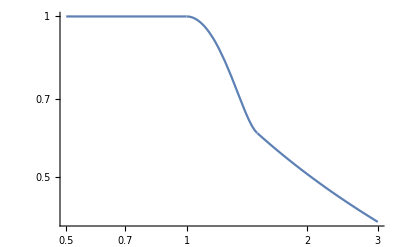

```mathematica
fitfunc[a1_,a2_,a3_,a4_,ma_]=a1+a2*ma+a3*ma^2+a4*ma^3;
coefsols=Solve[{fitfunc[a1,a2,a3,a4,1]==1&&(D[fitfunc[a1,a2,a3,a4,ma],ma]/.{ma->1})==0&&fitfunc[a1,a2,a3,a4,1.5]==(4*Pi)/(7*2*Log[1.5/0.34])&&(D[fitfunc[a1,a2,a3,a4,ma],ma]/.{ma->1.5})==(D[(4*Pi)/(7*2*Log[ma/0.34]),ma]/.{ma->1.5})},{a1,a2,a3,a4}];
αS[ma_]=Piecewise[{{1,ma≤1},{fitfunc[a1/.coefsols,a2/.coefsols,a3/.coefsols,a4/.coefsols,ma][[1]],1<ma≤1.5},{(4*Pi)/(7*2*Log[ma/0.34]),ma>1.5}}];
LogLogPlot[αS[ma],{ma,0.5,3}]
```

## ALP phenomenology (f_g = (g^-1)_a)

## Production probabilities

### From decays of B

```mathematica
(*Currently, Eqs. S67-68 from hhttps://arxiv.org/pdf/1811.03474.pdf are used for the br ratio*)
(*In the future, after discussing with the authors https://arxiv.org/pdf/2102.04474.pdf about some disagreement obtained after following their approach, the expression from this paper will be included instead*)
BrBtoa[ma_,fG_]=If[ma<mB-mK,Evaluate[1/fG^2 Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with gluon coupling/branching ratios/BrBtoa.dat"}],InterpolationOrder->1]][ma]],0];
PBtoALPatSPS[ma_,fG_]=(fbtobplusSPS+fbtob0SPS)*BrBtoa[ma,fG];
PBtoALPatFermilabBD[ma_,fG_]=(fbtobplusFermilabBD+fbtob0FermilabBD)*BrBtoa[ma,fG];
PBtoALPatLHC[ma_,fG_]=(fbtobplusLHC+fbtob0LHC)*BrBtoa[ma,fG];
PBtoALPatFCChh[ma_,fG_]=(fbtobplusLHC+fbtob0LHC)*BrBtoa[ma,fG];
pBtoALPfacility[ma_,fG_,facility_]:=Association[{{ma,fG,"FermilabBD"}-> PBtoALPatFermilabBD[ma,fG],{ma,fG,"SPS"}-> PBtoALPatSPS[ma,fG],{ma,fG,"LHC"}-> PBtoALPatLHC[ma,fG],{ma,fG,"FCC-hh"}-> PBtoALPatFCChh[ma,fG]}][{ma,fG,facility}]
```

### From mixing with light pseudoscalar mesons

{a0→-25.4899,a1→49.0191,a2→-29.4815,a3→5.70222}

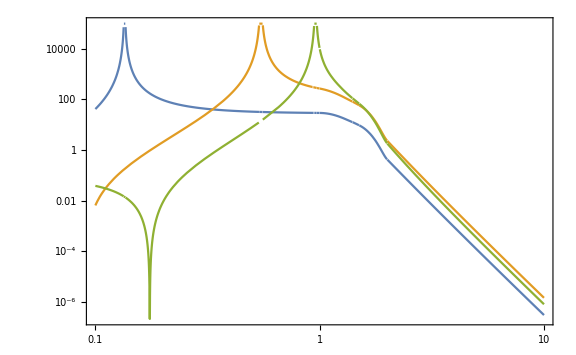

```mathematica
(*Mixing angles with light pseudoscalar mesons*)
(*Form-factors from 2201.05170,1811.03474*)
mascale=1.4;
funcFitFormFactor[ma_]=a0+a1*ma+a2*ma^2+a3*ma^3;
FormFactorLargema[ma_]=(mascale/ma)^4;
CoefficientScalings=
Solve[funcFitFormFactor[1.4]==1&&(D[funcFitFormFactor[ma],ma]/.{ma->1.4})==0&&funcFitFormFactor[2]==FormFactorLargema[2]&&(D[funcFitFormFactor[ma],ma]/.{ma->2})==(D[FormFactorLargema[ma],ma]/.{ma->2}),{a0,a1,a2,a3}][[1]]
FormFactorVMD[ma_]=Piecewise[{{1,ma≤1.4},{Evaluate[(funcFitFormFactor[ma]/.{a0->(a0/.CoefficientScalings),a1->(a1/.CoefficientScalings),a2->(a2/.CoefficientScalings),a3->(a3/.CoefficientScalings)})],1.4<ma<2},{(mascale/ma)^4,ma≥2 }}];
κmass[mq_]=1/(mq(1/mu+1/md+1/ms));
Γη=1.31*10^-6;
Γηpr=0.188*10^-3;
Kaπ0=(κmass[mu]-κmass[md])/2;
Kaη=-1/(√3)((κmass[mu]+κmass[md])(Cos[θηηpr]-√2 Sin[θηηpr])-κmass[ms]*(2Cos[θηηpr]+√2 Sin[θηηpr]))/2;
Kaηpr=-1/(√3)((κmass[mu]+κmass[md])(Sin[θηηpr]+√2 Cos[θηηpr])-κmass[ms]*(2Sin[θηηpr]-√2 Cos[θηηpr]))/2;
m2aπ0=0;
m2aη=-√6(mπ0^2/(mu+md))Sin[θηηpr]*κmass[1];
m2aηpr=√6(mπ0^2/(mu+md))Cos[θηηpr]*κmass[1];
cutoff=10^-20;
θaπ02[ma_,fG_]=αS[ma]^2/fG^2 FormFactorVMD[ma]^2 Min[(32*Pi^2 fπ(Kaπ0*ma^2+m2aπ0)/(√((ma^2-mπ0^2)^2+cutoff)(*+mπ0^2*Γπ0^2*)))^2,10^5];
θaη2[ma_,fG_]=αS[ma]^2/fG^2 FormFactorVMD[ma]^2 Min[(32*Pi^2 fπ(Kaη*ma^2+m2aη)/(√((ma^2-mη^2)^2+cutoff)(*+mπ0^2*Γπ0^2*)))^2,10^5];
θaηpr2[ma_,fG_]=αS[ma]^2/fG^2 FormFactorVMD[ma]^2 Min[(32*Pi^2 fπ(Kaηpr*ma^2+m2aηpr)/(√((ma^2-mηpr^2)^2+cutoff)(*+mπ0^2*Γπ0^2*)))^2,10^5];
LogLogPlot[{θaπ02[ma,1],θaη2[ma,1],θaηpr2[ma,1]},{ma,0.1,10},Frame->True,ImageSize->Large]
```

### Drell-Yan

```mathematica
σDrellYanData[file_]:=Block[{},
dat=Import[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with gluon coupling/branching ratios",file}],"Table"];
MinMaxMassesDrellYan=MinMax[dat[[All,1]]];
{MinMaxMassesDrellYan,If[MinMaxMassesDrellYan[[1]]≤ ma≤MinMaxMassesDrellYan[[2]],Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]+10^-90]}&/@dat,InterpolationOrder->1][Log10[ma]])],0]}
]
{{mDrellYanMinLHC,mDrellYanMaxLHC},σDrellYanpbLHCatLO[mV_]}=σDrellYanData["sigmaDrellYan-ALPgluon-LHC.txt"];
{{mDrellYanMinSPS,mDrellYanMaxSPS},σDrellYanpbSPSatLO[mV_]}=σDrellYanData["sigmaDrellYan-ALPgluon-SPS.txt"];
{{mDrellYanMinFermilabBD,mDrellYanMaxFermilabBD},σDrellYanpbFermilabBDatLO[mV_]}=σDrellYanData["sigmaDrellYan-ALPgluon-FermilabBD.txt"];
{PDrellYanFacility[ma_,fG_,Atarget_,"FermilabBD"],PDrellYanFacility[ma_,fG_,Atarget_,"SPS"],PDrellYanFacility[ma_,fG_,Atarget_,"LHC"],PDrellYanFacility[ma_,fG_,Atarget_,"FCC-hh"]}=1/fG^2*{σDrellYanpbFermilabBDatLO[ma]/σpNucleonInpb[Atarget],σDrellYanpbSPSatLO[ma]/σpNucleonInpb[Atarget],σDrellYanpbLHCatLO[ma]/(σppLHC//N),0};
```

## ALP lifetime and branching ratios

### Lifetimes

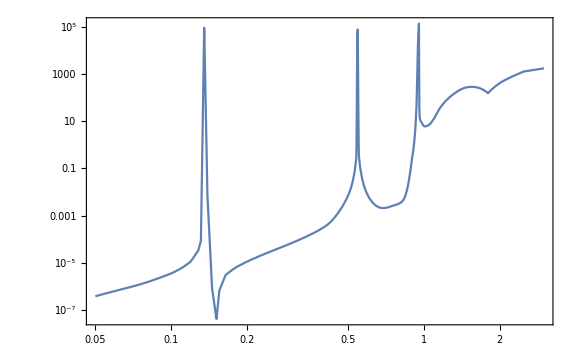

```mathematica
ΓALP[ma_,fG_]=1/fG^2 10^(Interpolation[{#[[1]],Log10[#[[2]]]}&/@Import[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with gluon coupling/decay widths/GammaTotALP.dat"}],"Table"],InterpolationOrder->1][ma]);
LogLogPlot[ΓALP[ma,1],{ma,0.05,3},Frame->True,ImageSize->Large]
(*Decay length of the ALP - following *)
cτALP[ma_,fG_]=chbar/ΓALP[ma,fG];
BrVisCharged[ma_]=Interpolation[Import[FileNameJoin[{NotebookDirectory[],"phenomenology/ALPs with gluon coupling/decay widths/BrChargedALP.dat"}],"Table"],InterpolationOrder->1][ma];
ldecayALP[ma_,fG_,Ea_]=cτALP[ma,fG]*(√(Ea^2-ma^2))/ma;
```

## Compilable interpolation function mapping one grid into another

### 3D to 3D

```mathematica
nd=3;
cf3=Module[{xgvars=Unique["xg"]&/@slist@@Range@nd,igvars=Unique["ig"]&/@slist@@Range@nd,tgvars=Unique["tg"]&/@slist@@Range@nd,ivars=Unique["i"]&/@slist@@Range@nd,svars=Unique["s"]&/@slist@@Range@nd,tvars=Unique["t"]&/@slist@@Range@nd,jvars=Unique["j"]&/@slist@@Range@nd},Inactivate[Compile[{seq@{xgvars,_Real,1},{y,_Real,nd}},Module[{seq@igvars,seq@tgvars,seq@ivars,seq@svars,seq@tvars},seq[igvars=Floor[xgvars]-UnitStep[xgvars-indexed@Dimensions@y]];
seq[tgvars=xgvars-igvars];
Table[seq[tvars=Compile`GetElement[tgvars,jvars]];
seq[ivars=Compile`GetElement[igvars,jvars]];
seq[svars=1.-tvars];
eval@Total[Times@@#[[All,1]] Compile`GetElement[y,Sequence@@#[[All,2]]]&/@Tuples@Transpose[{{svars,ivars},{tvars,ivars+1}},{2,3,1}]],seq@{jvars,Length@igvars}]],CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"],Except[seq|eval|indexed]]/.seq[expr_]:>RuleCondition@(Sequence@@Table[Inactivate[expr,Except[slist|indexed]]/.{l_slist:>l[[i]],indexed[l_]:>Inactive[Compile`GetElement][l,i]},{i,nd}])/.eval@expr_:>RuleCondition[Activate[expr/.slist->List]]]//Activate;
```

### 4D to 4D

```mathematica
nd=4;
cf4=Module[{xgvars=Unique["xg"]&/@slist@@Range@nd,igvars=Unique["ig"]&/@slist@@Range@nd,tgvars=Unique["tg"]&/@slist@@Range@nd,ivars=Unique["i"]&/@slist@@Range@nd,svars=Unique["s"]&/@slist@@Range@nd,tvars=Unique["t"]&/@slist@@Range@nd,jvars=Unique["j"]&/@slist@@Range@nd},Inactivate[Compile[{seq@{xgvars,_Real,1},{y,_Real,nd}},Module[{seq@igvars,seq@tgvars,seq@ivars,seq@svars,seq@tvars},seq[igvars=Floor[xgvars]-UnitStep[xgvars-indexed@Dimensions@y]];
seq[tgvars=xgvars-igvars];
Table[seq[tvars=Compile`GetElement[tgvars,jvars]];
seq[ivars=Compile`GetElement[igvars,jvars]];
seq[svars=1.-tvars];
eval@Total[Times@@#[[All,1]] Compile`GetElement[y,Sequence@@#[[All,2]]]&/@Tuples@Transpose[{{svars,ivars},{tvars,ivars+1}},{2,3,1}]],seq@{jvars,Length@igvars}]],CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"],Except[seq|eval|indexed]]/.seq[expr_]:>RuleCondition@(Sequence@@Table[Inactivate[expr,Except[slist|indexed]]/.{l_slist:>l[[i]],indexed[l_]:>Inactive[Compile`GetElement][l,i]},{i,nd}])/.eval@expr_:>RuleCondition[Activate[expr/.slist->List]]]//Activate;
```

# Specifying the experiment

```mathematica
SetDirectory[NotebookDirectory[]];
(*Parent directory*)
NotebookDirectory[]//ParentDirectory;
AcceptanceDirectory=FileNameJoin[{NotebookDirectory[],"Acceptances"}];
ExperimentDirectoriesList=Select[FileNames["*",AcceptanceDirectory,1],DirectoryQ];
(*List of available experiments (for which the geometry has been implemented)*)
ExperimentsListTemp=Table[FileNameTake[ExperimentDirectoriesList[[i]],-1],{i,1,Length[ExperimentDirectoriesList],1}];
ExperimentsListTemp2=Join[Partition[ExperimentsListTemp,1],Table[{TrueQ@FileExistsQ@FileNameJoin[{NotebookDirectory[],"Acceptances",ExperimentsListTemp[[i]],ToString@StringForm["Acceptance_``_for_ALP-gluon.m",ExperimentsListTemp[[i]]]}]},{i,1,Length[ExperimentsListTemp]}],2]
ExperimentsList=Select[ExperimentsListTemp2,#[[2]]==True&][[All,1]]//Sort
If[Length[ExperimentsList]==0,Print["No experiment is available, generate first the acceptance for the given experiment using module 1"]]
Print["Selected experiment:"]
dropdownDialog[list_,phrase_]:=DialogInput[{choice=""},Column[{TextCell[phrase],PopupMenu[Dynamic[choice],list],Button["OK",DialogReturn[choice]]}]]
SelectedExperiment=dropdownDialog[ExperimentsList,"Select the experiment:"]
```

(advSNDnear | True
ANUBIS-1 | True
ANUBIS-2 | True
ANUBIS-3 | True
ANUBIS-ceiling | False
ANUBIS-shaft-volume-1 | False
ANUBIS-shaft-volume-2 | False
ANUBIS-shaft-volume-3 | False
DarkQuest | False
DarkQuest-phase-2 | False
DUNE-ND-LAr | False
FACET | True
FACET-FCC | False
FASER | False
HIKE-phase2 | False
LHCb-far | False
LHCb-far-no-kinematics | False
LHCb-far-SciFi | False
MATHUSLA | True
NA62 | False
SHADOWS-latest | False
SHADOWS-LoI | True
SHADOWS-LoI-up-to-magnet | False
SHiP-ECN3 | True
SHiP-ECN3-alt | False
SNDatLHC | False)

{advSNDnear,ANUBIS-1,ANUBIS-2,ANUBIS-3,FACET,MATHUSLA,SHADOWS-LoI,SHiP-ECN3}

Selected experiment:

SHiP-ECN3

## Cross-sections, acceptances

```mathematica
dataAcceptances=Import[FileNameJoin[{FileNameJoin[{NotebookDirectory[],"Acceptances",SelectedExperiment,ToString@StringForm["Acceptance_``_for_ALP-gluon.m",SelectedExperiment]}]}],"MX"];//AbsoluteTiming
FacilityGivenExperiment=dataAcceptances[[1]];
ECALoption=dataAcceptances[[2]];
BrVis[ma_]=If[ECALoption=="False",BrVisCharged[ma],1];
FullAcceptanceData0=dataAcceptances[[3]];
{θminExpAll,θmaxExpAll}=MinMax[FullAcceptanceData0[[All,2]]];
{θminExp,θmaxExp}=MinMax[Select[FullAcceptanceData0,#[[6]]≠0&][[All,2]]];
{zminExp,zmaxExp}=MinMax[FullAcceptanceData0[[All,4]]];
AzimuthalAcceptanceData=DeleteDuplicatesBy[FullAcceptanceData0,{#[[2]],#[[4]]}&][[All,{2,4,5}]];//AbsoluteTiming
θGrid=DeleteDuplicates[AzimuthalAcceptanceData[[All,1]]];
zminmaxθdata=Table[MinMax[Select[AzimuthalAcceptanceData,#[[1]]==θGrid[[i]]&&#[[3]]≠0&][[All,2]]],{i,1,Length[θGrid],1}];
zminθ[θa_]=Interpolation[Join[Partition[θGrid,1],zminmaxθdata[[All,{1}]],2],InterpolationOrder->1][θa];
zmaxθ[θa_]=Interpolation[Join[Partition[θGrid,1],zminmaxθdata[[All,{2}]],2],InterpolationOrder->1][θa];
AzimuthalAcceptanceALPgluon[θa_,za_]=Interpolation[{#[[1]],#[[2]],#[[3]]}&/@AzimuthalAcceptanceData,InterpolationOrder->1][θa,za]
DecAccDataLogarithmizedComp=Hold@Compile[{{FullAcceptanceData,_Real,2}},{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]],Log10[#[[6]]]}&/@FullAcceptanceData]//ReleaseHold;
DecayAcceptanceALPgluon[ma_,θa_,Ea_,za_]=BrVis[ma]*10^(Interpolation[DecAccDataLogarithmizedComp[FullAcceptanceData0],InterpolationOrder->1][Log10[ma],Log10[θa],Log10[Ea],Log10[za]]);//AbsoluteTiming
(*Interpolation for the full acceptance*)
acccomp=Hold@Compile[{{data,_Real,2}},{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]],If[#[[5]]*#[[6]]==0,-90,Log10[#[[5]]*#[[6]]]]}&/@SortBy[data,{#[[1]],#[[2]],#[[3]],#[[4]]}&]]//ReleaseHold;
(*Interpolation for the full acceptance*)
FullAcceptanceData=acccomp[FullAcceptanceData0];//AbsoluteTiming
FullAcceptanceALPgluon[ma_,θa_,Ea_,za_]=10^(Interpolation[FullAcceptanceData,InterpolationOrder->1][Log10[ma],Log10[θa],Log10[Ea],Log10[za]]);//AbsoluteTiming
CrossSectionData=dataAcceptances[[4]]//Transpose;
χprod["B"]=Select[CrossSectionData,#[[1]]=="χ_(b or OverscriptBox[b, _])"&][[1]][[2]];
χprod["π^0"]=Select[CrossSectionData,#[[1]]=="χ_(π^0)"&][[1]][[2]];
χprod["η"]=Select[CrossSectionData,#[[1]]=="χ_η"&][[1]][[2]];
χprod["η'"]=Select[CrossSectionData,#[[1]]=="χ_η'"&][[1]][[2]];
AtargetVal=Select[CrossSectionData,#[[1]]=="A_target"&][[1]][[2]];
{{"χ_(b or OverscriptBox[b, _])","χ_(π^0)","χ_η","χ_η'"},{χprod["B"],χprod["π^0"],χprod["η"],χprod["η'"]}}//TableForm
NpotGivenExperiment=Select[CrossSectionData,#[[1]]=="N_PoT"&][[1]][[2]]//N;
infoDialog[Row[{"The number of proton collisions is ", NpotGivenExperiment,". You may change it at the stage of computing the sensitivities"}]]
Row[{"Search for ALPs coupled to gluons at ", SelectedExperiment, " located at ",FacilityGivenExperiment,". N_collisions = ",NpotGivenExperiment}]
{{"Quantity","θ_min, rad","θ_max, rad","θ_min(ϵ_dec), rad","θ_max(ϵ_dec), rad","z_min, m","z_max, m"},{"Description","Min angle covered by experiment","Max angle covered by experiment","Min angle where ϵ_decay≠0","Max angle where ϵ_decay≠0","Min long. displacement of the decay volume","Max long. displacement of the decay volume"},{"Value",θminExpAll,θmaxExpAll,θminExp,θmaxExp,zminExp,zmaxExp}}//TableForm
```

{0.221442,Null}

{1.21357,Null}

InterpolatingFunction[…](θa,za)

{1.2984,Null}

{0.846694,Null}

{0.842971,Null}

χ_(b or OverscriptBox[b, _]) | χ_(π^0) | χ_η | χ_η'
5.42908×10^-7 | 6.2 | 0.8 | 0.079

Search for ALPs coupled to gluons at SHiP-ECN3 located at SPS. N_collisions = 6.×10^20

Quantity | θ_min, rad | θ_max, rad | θ_min(ϵ_dec), rad | θ_max(ϵ_dec), rad | z_min, m | z_max, m
Description | Min angle covered by experiment | Max angle covered by experiment | Min angle where ϵ_decay≠0 | Max angle where ϵ_decay≠0 | Min long. displacement of the decay volume | Max long. displacement of the decay volume
Value | 0.00001 | 0.0449146 | 0.00001 | 0.0449146 | 32. | 82.

# Number of events

## Angle-energy distributions for the given experiment

## ALP distributions

```mathematica
ALPDistributionFileNames:=Association[{"SPS"->{"DoubleDistr-ALPgluon-From-B-SPS.dat","DoubleDistr-ALPgluon-mixing-from-Pi0-SPS.dat","DoubleDistr-ALPgluon-mixing-from-Eta-SPS.dat","DoubleDistr-ALPgluon-mixing-from-EtaPr-SPS.dat"},"LHC"->{"DoubleDistr-ALPgluon-From-B-LHC.dat","DoubleDistr-ALPgluon-mixing-from-Pi0-LHC.dat","DoubleDistr-ALPgluon-mixing-from-Eta-LHC.dat","DoubleDistr-ALPgluon-mixing-from-EtaPr-LHC.dat"},"FermilabBD"->{"DoubleDistr-ALPgluon-From-B-FermilabBD.dat","DoubleDistr-ALPgluon-mixing-from-Pi0-FermilabBD.dat","DoubleDistr-ALPgluon-mixing-from-Eta-FermilabBD.dat","DoubleDistr-ALPgluon-mixing-from-EtaPr-FermilabBD.dat"}}]
ALPDistributionFileNamesGivenExp=ALPDistributionFileNames[FacilityGivenExperiment];
Do[If[!TrueQ@FileExistsQ@FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with gluon coupling/",ALPDistributionFileNamesGivenExp[[j]]}],Print[ALPDistributionFileNamesGivenExp[[j]]," does not exist Generate it using module 2!"]
],{j,1,Length[ALPDistributionFileNamesGivenExp],1}]
Clear[j]
```

### Importing distributions

{0.983745,Null}

{1.98106,Null}

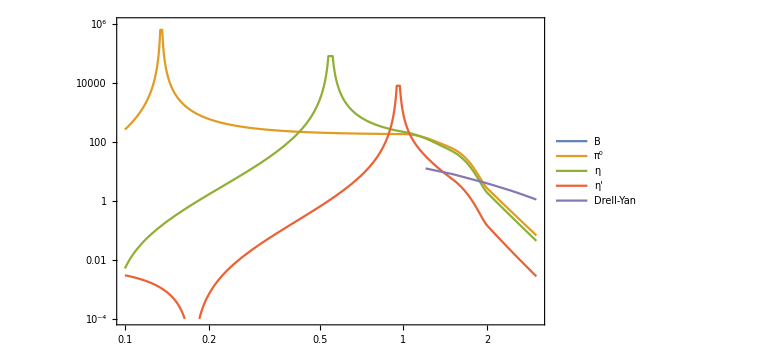

```mathematica
dataDistr[filename_]:=Import[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with gluon coupling/",filename}],"Table"]
{χXtimesχXtoALP[ma_,fG_,"B"],χXtimesχXtoALP[ma_,fG_,"π^0"],χXtimesχXtoALP[ma_,fG_,"η"],χXtimesχXtoALP[ma_,fG_,"η'"]}={χprod["B"]*pBtoALPfacility[ma,fG,FacilityGivenExperiment],χprod["π^0"]*θaπ02[ma,fG],χprod["η"]*θaη2[ma,fG],χprod["η'"]*θaηpr2[ma,fG]};
{DataDistrALPgluon["B"],DataDistrALPgluon["π^0"],DataDistrALPgluon["η"],DataDistrALPgluon["η'"]}=dataDistr[ALPDistributionFileNamesGivenExp[[#]]]&/@{1,2,3,4};//AbsoluteTiming
ProductionList={"B","π^0","η","η'"};
ExportList:=Association[{"π^0"->"Pi0","η"->"Eta","η'"->"Etapr","B"->"B","Drell-Yan"-> "Drell-Yan"}]
If[FacilityGivenExperiment≠"FCC-hh",
ProductionList=Join[ProductionList,{"Drell-Yan"}];
χXtimesχXtoALP[ma_,fG_,"Drell-Yan"]=PDrellYanFacility[ma,fG,AtargetVal,FacilityGivenExperiment];
DataDistrALPgluon["Drell-Yan"]=Import[FileNameJoin[{NotebookDirectory[],"spectra/New physics particles spectra/ALPs with gluon coupling/Pregenerated/",ToString@StringForm["DoubleDistrALPsGluonDrellYan-``.txt",Sequence@@{FacilityGivenExperiment}]}],"Table"];
]
mminϵDec=10^FullAcceptanceData[[All,1]]//Min;
Do[DoubleDistrALP[ma_,θa_,Ea_,prod]=10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]],Log10[#[[4]]+10^-80]}&/@DataDistrALPgluon[prod],InterpolationOrder->1][Log10[ma],Log10[θa],Log10[Ea]]);
mlistALPgluonTemp=DeleteDuplicates[DataDistrALPgluon[prod][[All,1]]];
mlistALPgluonTemp1=If[mminϵDec>(mlistALPgluonTemp//Min),Join[{mminϵDec},Select[mlistALPgluonTemp,#>1.001mminϵDec&]],mlistALPgluonTemp];
mlistALPgluon[prod]=mlistALPgluonTemp1;
{mamin[prod],mamax[prod]}=MinMax[mlistALPgluon[prod]];
,{prod,ProductionList}]//AbsoluteTiming
LogLogPlot[Evaluate[Table[χXtimesχXtoALP[ma,1,prod],{prod,ProductionList}]],{ma,0.1,3},Frame->True,ImageSize->Large,PlotRange->{All,{10^-4,10^6}},PlotLegends->Placed[Style[#,15]&/@ProductionList,Right]]
```

### Determining min/max energies of scalars for the given polar angle. Needed for stability of Monte-Carlo integration

#### Common definition

InterpolatingFunction::dmval: Input value {0.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

{6.6551,Null}

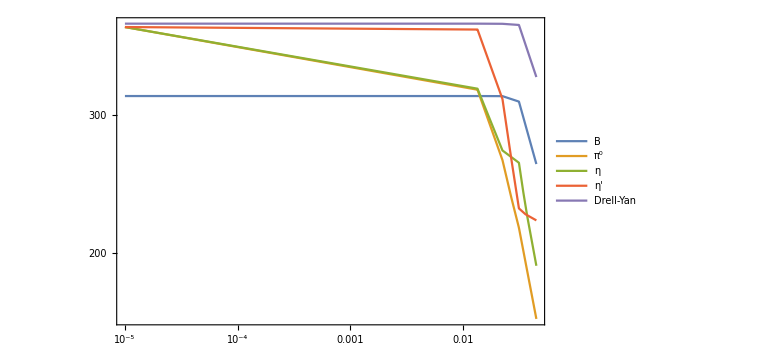

```mathematica
EfromXmax[mass_,data_,LogMin_]:=Module[{distr},
datt=Select[data,#[[1]]==mass&];
EmaxVal=datt[[All,3]]//Max;
θlist=Table[x,{x,θminExp,θmaxExp,(θmaxExp-θminExp)/5}];
distr[θa_,Ea_]=Abs[Evaluate[Interpolation[{#[[2]],#[[3]],#[[4]]+10^-90}&/@datt,InterpolationOrder->1][θa,Ea]]];
DoubleDistrIntList[i_]:=Interpolation[ParallelTable[{Ea,Quiet[NIntegrate[distr[θa,Ea],{θa,θlist[[i]],θlist[[i+1]]},Method->"AdaptiveMonteCarlo"]]},{Ea,Table[10^x,{x,Log10[1.1*mass],Log10[EmaxVal],(Log10[EmaxVal]-Log10[1.1*mass])/50.}]}],InterpolationOrder->1][Ea];
θadistrlist[Ea_]=Table[{(θlist[[i]]+θlist[[i+1]])/2,DoubleDistrIntList[i]},{i,1,Length[θlist]-1,1}];
θEmaxList=Table[{θadistrlist[Ea][[i]][[1]],SortBy[Table[{Ea,θadistrlist[Ea][[i]][[2]]},{Ea,mass,EmaxVal,1}],-#[[2]]&][[1]][[1]]},{i,1,Length[θadistrlist[Ea]],1}];
θEmaxListInt[θa_]=Interpolation[θEmaxList,InterpolationOrder->1][θa];
NormVals=Table[NIntegrate[θadistrlist[Ea][[i]][[2]]+10^-90.,{Ea,mass,EmaxVal},Method->"InterpolationPointsSubdivision"],{i,1,Length[θadistrlist[Ea]],1}];
cdf[es_,i_]:=1-1/NormVals[[i]] NIntegrate[θadistrlist[Ea][[i]][[2]],{Ea,mass,es},Method->"InterpolationPointsSubdivision"];
cdftab[Ea_]=Table[{θadistrlist[Ea][[i]][[1]],Interpolation[ParallelTable[{10^es,Quiet[cdf[10^es,i]]},{es,Log10[mass],Log10[EmaxVal],(Log10[EmaxVal]-Log10[mass])/50}],InterpolationOrder->1][Ea]},{i,1,Length[θadistrlist[Ea]],1}];
logmin[θa_]=LogMin;
Estart[θa_]=Min[2*θEmaxListInt[θa],0.9*EmaxVal];
Emaxv[i_]:=If[NormVals[[i]]<10^-15,mass,10^(Ea/.FindRoot[Log10[cdftab[10^Ea][[i]][[2]]]==logmin[θEmaxList[[i]][[1]]],{Ea,Log10[Estart[θEmaxList[[i]][[1]]]],Log10[θEmaxList[[i]][[2]]],Log10[EmaxVal]}])];
tabtemp=Table[{θEmaxList[[i]][[1]],Emaxv[i]},{i,1,Length[θEmaxList],1}];
tab=Join[{{θminExp,tabtemp[[1]][[2]]}},Drop[Drop[tabtemp,1],-1],{{θmaxExp,tabtemp[[-1]][[2]]}}];
10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]]}&/@tab,InterpolationOrder->1][Log10[θa]])
]
EamaxBlock[data_,logmin_]:=Module[{mlist},
mlist=Drop[data[[All,1]],-1];
EmaxTemp[ma_,θa_]=Max[ma,EfromXmax[mlist[[1]],data,logmin],EfromXmax[mlist[[-1]],data,logmin]];
θlist=Table[x,{x,θminExp,θmaxExp,(θmaxExp-θminExp)/10}];
10^(Interpolation[{#[[1]],Log10[#[[2]]],Log10[#[[3]]]}&/@Flatten[Table[{ma,θa,EmaxTemp[ma,θa]},{ma,mlist[[1]],mlist[[-1]],(mlist[[-1]]-mlist[[1]])/10},{θa,θlist}],{1,2}],InterpolationOrder->1][ma,Log10[θa]])
]
Do[Eamax[ma_,θa_,prod]=EamaxBlock[DataDistrALPgluon[prod],-7],{prod,ProductionList}];//AbsoluteTiming
LogLogPlot[Evaluate[Table[Eamax[1.5,θa,prod],{prod,ProductionList}]],{θa,θminExp,θmaxExp},Frame->True,ImageSize->Large,PlotRange->{All,All},PlotLegends->Placed[Style[#,15]&/@ProductionList,Right]]
```

## Number of events

## Definitions

### Grids for the initial data with acceptances and distributions

```mathematica
(*Grid Subscript[m, S], Subscript[θ, S], Subscript[E, S], Subscript[z, S] for the initial acceptance data, logarithmized*)
InGridmϵ=DeleteDuplicates[FullAcceptanceData[[All,1]]];
InGridθϵ=DeleteDuplicates[FullAcceptanceData[[All,2]]];
InGridEϵ=DeleteDuplicates[FullAcceptanceData[[All,3]]];
InGridzϵ=DeleteDuplicates[FullAcceptanceData[[All,4]]];
(*Array of values of the initial acceptance data, reshaped*)
ϵvals=ArrayReshape[FullAcceptanceData[[All,5]],{Length[InGridmϵ],Length[InGridθϵ],Length[InGridEϵ],Length[InGridzϵ]}];
ϵazValscomp=Compile[{{data,_Real,2}},Table[If[data[[i]][[5]]==0,-90.,Log10[data[[i]][[5]]]],{i,1,Length[data],1}],CompilationTarget->"C",RuntimeOptions->"Speed"];
ϵazvals=ArrayReshape[ϵazValscomp[FullAcceptanceData0],{Length[InGridmϵ],Length[InGridθϵ],Length[InGridEϵ],Length[InGridzϵ]}];
(*_________________________________________________________________*)
(*Grid Subscript[m, S], Subscript[θ, S], Subscript[E, S] for the initial FIP distribution data, logarithmized*)
DataLogarithmiedComp=Hold@Compile[{{data,_Real,2}},Table[If[data[[i]][[4]]==0,-90.,Log10[data[[i]][[4]]]],{i,1,Length[data],1}],CompilationTarget->"C",RuntimeOptions->"Speed"]//ReleaseHold
BlockGridsValsDistr[ProdChannel_]:=Module[{GridIn,vals},
GridIn=Log10[DeleteDuplicates[DataDistrALPgluon[ProdChannel][[All,#]]]&/@{1,2,3}];
vals=ArrayReshape[DataLogarithmiedComp[DataDistrALPgluon[ProdChannel]],{Length[GridIn[[1]]],Length[GridIn[[2]]],Length[GridIn[[3]]]}];
{GridIn,vals}
]
Do[{GridInFinal[prod],DistrVals[prod]}=BlockGridsValsDistr[prod],{prod,ProductionList}];//AbsoluteTiming
```

CompiledFunction[…]

{0.0511758,Null}

### Grid to be used to calculate the number of events

```mathematica
(*Grid Subscript[θ, S], Subscript[z, S] for the final acceptance data, logarithmized*)
OutGridθfinal=(*InGridθϵ*)Log10[Table[x,{x,10^Min[InGridθϵ],10^Max[InGridθϵ],(10^Max[InGridθϵ]-10^Min[InGridθϵ])/30}]];
OutGridzfinal=Log10[Table[x,{x,10^InGridzϵ[[1]],10^InGridzϵ[[-1]],Min[(10^InGridzϵ[[-1]]-10^InGridzϵ[[1]])/5,Max[0.5,(10^InGridzϵ[[-1]]-10^InGridzϵ[[1]])/30]]}]](*InGridzϵ*);
ΔxVals[list_]:=Join[{(list[[2]]-list[[1]])/2},Table[list[[i]]-list[[i-1]],{i,2,Length[list],1}]];
Δθvals=ΔxVals[10^OutGridθfinal];
Δzvals=ΔxVals[10^OutGridzfinal];
(*Final energy grid. Mass- and production channel-dependent*)
StepEtemp[Efip_]=Piecewise[{{0.3,Efip≤2.5},{0.5,2.5<Efip<35},{2,35≤Efip≤50},{4,50<Efip<160},{5,160≤Efip<300},{40,300≤Efip<700},{50,700≤Efip<2000},{200,2000≤Efip<4000},{400,4000≤Efip<7000},{500,7000≤Efip≤50000}}];
OutGridEnergy[m_,ProdChannel_]:=Block[{},
With[{start=1.01m,end=Eamax[m,θminExp,ProdChannel]},
Log10[NestWhileList[#+StepEtemp[#]&,start,#≤end&,1,∞,-1]]]//N
]
ΔxValsTotComp=Hold@Compile[{{Δθvals,_Real,1},{ΔEvals,_Real,1},{Δzvals,_Real,1}},Table[{Δθvals[[i]]*ΔEvals[[j]]*Δzvals[[k]]},{i,1,Length[Δθvals]},{j,1,Length[ΔEvals]},{k,1,Length[Δzvals]}],CompilationTarget->"C",RuntimeOptions->"Speed"]//ReleaseHold;
```

### Code that computes the number of events - using the mapping method

#### Grid for distribution times acceptance

```mathematica
(*Block that computes the grid Subscript[θ, S],Subscript[E, S],Subscript[z, S], Subscript[ϵ, Full]×Subscript[f, Subscript[θ, S],Subscript[E, S]]*)
TableIntegrandDiscret[m_,ProdChannel_,ϵDecOp_]:=Block[{},
OutGridEfinal=OutGridEnergy[N[m],ProdChannel];
ΔEvals=ΔxVals[10^OutGridEfinal];
ΔxValsTot=Flatten[ΔxValsTotComp[Δθvals,ΔEvals,Δzvals],{1,2,3}];
OutGridFinal=Tuples[{{Log10[N[m]]},OutGridθfinal,OutGridEfinal,OutGridzfinal}];
OutGridFinal1=10^OutGridFinal[[All,{2,3,4}]];
gϵ={InGridmϵ,InGridθϵ,InGridEϵ,InGridzϵ};
xgϵ={{Log10[N[m]]},OutGridθfinal,OutGridEfinal,OutGridzfinal};
xigϵ=MapThread[Interpolation[Transpose@{#,Range@Length@#},InterpolationOrder->1][#2]&,{gϵ,xgϵ}];
ϵResult=10^Flatten@cf4[Sequence@@xigϵ,If[ϵDecOp=="True",ϵvals,ϵazvals]];
gDistr={GridInFinal[ProdChannel][[1]],GridInFinal[ProdChannel][[2]],GridInFinal[ProdChannel][[3]]};
xgDistr={{Log10[N[m]]},OutGridθfinal,OutGridEfinal};
xigDistr=MapThread[Interpolation[Transpose@{#,Range@Length@#},InterpolationOrder->1][#2]&,{gDistr,xgDistr}];
DistrResult=10^Flatten@cf3[Sequence@@xigDistr,DistrVals[ProdChannel]];
TabTemp0=Join[OutGridFinal1,List/@Flatten[DistrResult Partition[ϵResult,Length[OutGridzfinal]]],ΔxValsTot,2]
]
```

#### Convoluting acceptances with pre-factor

```mathematica
(*Values Subscript[f, FIP]×Subscript[ϵ, FIP]×Exp[-Subscript[z, FIP]/(cos(Subscript[θ, FIP])Subscript[cτ, FIP] Subscript[p, FIP]/Subscript[m, FIP])]/(cos(Subscript[θ, FIP])Subscript[cτ, FIP] Subscript[p, FIP]/Subscript[m, FIP])×Subscript[ϵ, decay] Subscript[Δz, FIP] Subscript[ΔE, FIP] Subscript[Δθ, FIP] for the grid of values Subscript[θ, FIP], Subscript[E, FIP], Subscript[z, FIP] fixed values of Subscript[cτ, FIP] and Subscript[m, FIP]*)
tableprefac=Hold@Compile[{{tabb,_Real,1},{m,_Real},{cτ,_Real},{decProb,_Integer}},Module[{angles,energies,zv,values,Δs,prefactor},
values=Compile`GetElement[tabb,4];
Δs=Compile`GetElement[tabb,5];
If[decProb==1,
angles=Compile`GetElement[tabb,1];
energies=Compile`GetElement[tabb,2];
zv=Compile`GetElement[tabb,3];
prefactor=Exp[-zv/(Cos[angles]*cτ*(√(energies^2-m^2))/m)]/(Cos[angles]*cτ*(√(energies^2-m^2))/m),prefactor=1.];
prefactor*Δs*values],CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True",RuntimeAttributes->{Listable}]//ReleaseHold;
(*Summation of the values above*)
sumcompile=Hold@Compile[{{tabcτm,_Real,1}},Total[tabcτm],CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True"]//ReleaseHold;
{mminϵ,mmaxϵ}=10^MinMax[InGridmϵ]
```

{0.02,5.}

#### Acceptances

```mathematica
FactorANUBISceiling=If[SelectedExperiment=="ANUBIS-ceiling",2,1];
AcceptanceDiscret[m_,ProdChannel_,ϵdecOp_,decProb_]:=Module[{NevDiscret,NpotTimesχval},
If[Max[mamin[ProdChannel],mminϵ]<m<Min[mamax[ProdChannel],mmaxϵ],
integrandtab=TableIntegrandDiscret[m,ProdChannel,ϵdecOp];
brvis=If[ϵdecOp==1,BrVis[m],1];
(*Test lifetime for the acceptance*)
cτacc=10^9;
(*Prefactor for the acceptance. If only azimuthal and *)
prefacacc=If[decProb==1,cτacc,1/(zmaxExp-zminExp)];
accdiscret=If[brvis!=0,FactorANUBISceiling*brvis*prefacacc*sumcompile[tableprefac[integrandtab,m,cτacc,decProb]],0],accdiscret=0];
accdiscret
]
```

## Acceptances and approximate lower/upper bounds computation

```mathematica
Do[mlistAcceptance[prod]=Join[Table[m,{m,1.01Max[mamin[prod],mminϵ],0.95Min[mamax[prod],mmaxϵ],Min[(0.95Min[mamax[prod],mmaxϵ]-1.01Max[mamin[prod],mminϵ])/20,2]}],{0.99Min[mamax[prod],mmaxϵ]}],{prod,ProductionList}];
Do[ϵGeomTabs[prod]=Table[{m,AcceptanceDiscret[m,prod,"False",0],AcceptanceDiscret[m,prod,"True",0],AcceptanceDiscret[m,prod,"False",1],AcceptanceDiscret[m,prod,"True",1]},{m,mlistAcceptance[prod]}],{prod,ProductionList}];//AbsoluteTiming
PlotAcc[ProdChannel_]:=ListLogPlot[{ϵGeomTabs[ProdChannel][[All,{1,2}]],ϵGeomTabs[ProdChannel][[All,{1,3}]],ϵGeomTabs[ProdChannel][[All,{1,4}]],ϵGeomTabs[ProdChannel][[All,{1,5}]]},FrameStyle->Directive[Black, 22],PlotStyle->{{Thickness[0.003],Blue},{Thickness[0.003],Darker@Red},{Thickness[0.003],Darker@Darker@Green},{Thickness[0.003],Black}},GridLines->Automatic,PlotRange->{MinMax[ϵGeomTabs[ProdChannel][[All,1]]],{0.9Min[Min[ϵGeomTabs[ProdChannel][[All,4]]],Min[ϵGeomTabs[ProdChannel][[All,3]]]],1.1Max[Max[ϵGeomTabs[ProdChannel][[All,2]]],Max[ϵGeomTabs[ProdChannel][[All,4]]]]}},Joined->True,Frame->True,ImageSize->Large,FrameLabel->{"m [GeV]","Acceptance"},PlotLabel-> Style[Row[{"From ",ProdChannel}], 20, Black],PlotLegends->Placed[{Style[#, 18]&/@{"<ϵ_FIP>","<ϵ_FIPϵ_decay>","cτ<ϵ_FIPP_decay>","cτ<ϵ_FIPP_decayϵ_decay>"}},{0.75,0.2}]]
Style[Row[Evaluate[Table[PlotAcc[prod],{prod,ProductionList}]]],ImageSizeMultipliers->{1,1,1,1}]
Do[FilenameAcceptance[prod]=ToString@StringForm["Acceptance_ALP-gluon_at_``_From_``.dat",Sequence@@{SelectedExperiment,ExportList[prod]}];
Export[FileNameJoin[{NotebookDirectory[],"Auxiliary data/ALPs with gluon coupling",SelectedExperiment,FilenameAcceptance[prod]}],ϵGeomTabs[prod][[All,{1,2,4,5}]],"Table"]
,{prod,ProductionList}]
```

### Rough estimates of the upper and lower bounds

#### Definitions

```mathematica
Do[fGMinusOneminEstimate[ma_,prod]=((NpotGivenExperiment*χXtimesχXtoALP[ma,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,5}]],InterpolationOrder->1][ma]*(zmaxExp-zminExp))/(2.3ldecayALP[ma,1,Ea] ma/(√(Ea^2-ma^2))))^(-1/4);
fGMinusOnemaxEstimate[ma_,prod]=(Abs[Re[Evaluate[-ProductLog[-1,-2.3*b/a]/b/.{a-> NpotGivenExperiment*χXtimesχXtoALP[ma,1,prod]*Interpolation[ϵGeomTabs[prod][[All,{1,3}]],InterpolationOrder->1][ma],b->zminExp/ldecayALP[ma,1,Eamax[0.5,θminExp,prod]]}]]])^(1/2),{prod,ProductionList}]
LogLogPlot[{0.3fGMinusOneminEstimate[ma,"π^0"],1.8fGMinusOnemaxEstimate[ma,"π^0"]},{ma,0.3,2.6},Frame->True,ImageSize->Large]
```

## Number of events

### Fast

```mathematica
FactorLowerBound=If[MemberQ[{"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"},SelectedExperiment]==True,0.1,0.3];
NeventsDiscret[m_,ProdChannel_,fGlist_]:=Module[{NevDiscret,NpotTimesχval,zshift},
If[Max[mamin[ProdChannel],mminϵ]<m<Min[mamax[ProdChannel],mmaxϵ],
integrandtab=TableIntegrandDiscret[m,ProdChannel,"True"];
NpotTimesχval[fG_]=NpotGivenExperiment*χXtimesχXtoALP[m,fG^-1,ProdChannel];
{lowerbound,upperbound}={fGMinusOneminEstimate[m,ProdChannel],fGMinusOnemaxEstimate[m,ProdChannel]};
brvis=BrVis[m];
NevDiscret[fG_]:=If[0.1lowerbound<fG<(*1.5*)2upperbound,NpotTimesχval[fG]*brvis*sumcompile[tableprefac[integrandtab,m,cτALP[m,fG^-1],1]],0];
Table[{m,fGlist[[i]],NevDiscret[fGlist[[i]]]},{i,1,Length[fGlist],1}],Table[{m,fGlist[[i]],0},{i,1,Length[fGlist],1}]]
]
```

### Slow, using built-in Mathematica functions Interpolation, NIntegrate

```mathematica
(*Differential decay probability 1/ldecay Exp[-l/ldecay], where l is expressed in terms of the longitudinal displacement z and polar angle θ as z/cosθ*)
(*Differential decay probability (1/ldecay)Exp[-l/ldecay], where l is expressed in terms of the longitudinal displacement z and polar angle θ as z/cosθ*)
PdecayDensity[ma_,fG_,θa_,Ea_,za_]=Exp[-za/(Cos[θa]*ldecayALP[ma,fG,Ea])]/(Cos[θa]*ldecayALP[ma,fG,Ea]);
(*The integrand determining the differential rate for events*)
Do[IntegrandALP[ma_,fG_,θa_,Ea_,za_,prod]=DoubleDistrALP[ma,θa,Ea,prod]*PdecayDensity[ma,fG,θa,Ea,za]*AzimuthalAcceptanceALPgluon[θa,za]*DecayAcceptanceALPgluon[ma,θa,Ea,za],{prod,ProductionList}]
IntegralALP[ma_,fG_,ProdChannel_]:=NIntegrate[Abs[IntegrandALP[ma,fG,θa,Ea,za,ProdChannel]],{θa,θminExp,θmaxExp},{Ea,ma,Eamax[ma,θa,ProdChannel]},{za,zminθ[θa],zmaxθ[θa]},Method->"AdaptiveMonteCarlo"]
Nevents[ma_,ga_,ProdChannel_]:=If[mamin[ProdChannel]≤ma≤mamax[ProdChannel]&&BrVis[ma]!=0,If[0.1fGMinusOneminEstimate[ma,ProdChannel]<ga<2fGMinusOnemaxEstimate[ma,ProdChannel],NpotGivenExperiment*χXtimesχXtoALP[ma,ga^-1,ProdChannel]*IntegralALP[ma,ga^-1,ProdChannel],0],0]
```

#### Test

```mathematica
(*This is a comparison between the slow and fast integration methods. For the selected mass and production channel, the numbers of events obtained using the methods should agree within 10%*)
(*If the agreement is worse, there may be a few reasons*)
(*1) The grid for the fast method is not dense enough. Try to increase the grid density (OutGridθfinal, OutGridEfinal, OutGridzfinal) to see whether the agreement improves. Sometimes, even a slightly denser grid for e.g. z may lead to a significant improvement in the agrement*)
(*2) The Monte-Carlo integrator for the slow method fails to evaluate properly; this may happen if the range of the integration over energies is too large compared to the domain where most of the events actually are (off-axis experiments such as MATHUSLA and ANUBIS). Another symptom is that for the given mass and coupling the integral "jumps", i.e., returns values with large error*)
mtest=0.7;
ProdTest="B";
galist=(*{10^-12,3*10^-12,5*10^-12,10^-11,5*10^-11,10^-10,5*10^-10,10^-9,5*10^-9,10^-8,2*10^-8,4*10^-8,10^-7,5*10^-7,6*10^-7,7*10^-7,8*10^-7,9*10^-7,10^-6,2*10^-6}//N*)Table[10^x,{x,-12.,-3.,0.3}];
dat1=NeventsDiscret[mtest,ProdTest,galist];//AbsoluteTiming
dat2=ParallelTable[{galist[[i]],cτALP[mtest,galist[[i]]],Nevents[mtest,galist[[i]],ProdTest]},{i,1,Length[galist],1}];//AbsoluteTiming
Join[dat1,dat2[[All,{3,2}]],2]//TableForm
```

### Differential number of events

```mathematica
(*The same as tableprefac but also including the grid*)
tableGridPrefac=Hold@Compile[{{tabb,_Real,2},{mS,_Real},{cτ,_Real}},{#[[1]],#[[2]],#[[3]],(Exp[-#[[3]]/(Cos[#[[1]]]*cτ*((√((#[[2]])^2-mS^2))/mS))]/(Cos[#[[1]]]*cτ*((√((#[[2]])^2-mS^2))/mS)))#[[4]]*#[[5]]}&/@tabb,CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True",RuntimeAttributes->{Listable}]//ReleaseHold;
(*Summation returning the differential number of events X, df/dX *)
NdiffCompiled=Hold@Compile[{{tabNdiff,_Real,2},{GridQuantity,_Real,1},{LengthPerVariable,_Integer},{NPoTtimesPprod,_Real}},Table[{tabNdiff[[LengthPerVariable*(i-1)+1]][[1]],NPoTtimesPprod*Sum[tabNdiff[[LengthPerVariable*(i-1)+j]][[4]],{j,1,LengthPerVariable,1}]},{i,1,Length[GridQuantity],1}],CompilationTarget->"C",RuntimeOptions->"Speed",Parallelization->"True"]//ReleaseHold
(*Variable = "E_X","x_x","θ_X". The number belongs to the column in the tabulated data*)
iVal:=Association[{"E_X" ->2,"θ_X"->1,"x_x"->3}]
(*Differential number of events*)
NeventsDifferentialDiscret[m_,ProdChannel_,ga_,Variable_]:=Module[{NpotTimesχval},
ival=iVal[Variable];
NpotTimesχval=NpotGivenExperiment*χXtimesχXtoALP[m,ga^-1,ProdChannel];
tablegrid0=TableIntegrandDiscret[m,ProdChannel,"True"];
Δxvals:=Association[{"E_X"->ΔEvals,"θ_X"-> Δθvals,"x_X"-> Δzvals}];
Δxval=Δxvals[Variable];
cτVal=cτALP[m,ga^-1];
brvis=BrVis[m];
ilist=DeleteDuplicates[{ival,1,2,3}];
tablegrid1=SortBy[{#[[ilist[[1]]]],#[[ilist[[2]]]],#[[ilist[[3]]]],#[[4]]}&/@tableGridPrefac[tablegrid0,m,cτVal],{#[[1]],#[[2]],#[[3]]}&];
GridQuantity=tablegrid1[[All,1]]//DeleteDuplicates;
LengthPerVariable=Length[tablegrid1]/Length[GridQuantity];
tab1=NdiffCompiled[tablegrid1,GridQuantity,LengthPerVariable,NpotTimesχval*brvis];
Join[tab1[[All,{1}]],Partition[tab1[[All,2]]*Δxval^-1,1],2]
]
mvaltest=0.7;
gatest=10^-7;
quantity="E_X";
LegendX:=Association[{"E_X"->"E_a [GeV]","θ_X"->"θ_a [rad]","x_X"-> "z_a [m]"}]
LegendY:=Association[{"E_X"->"dN_ev/dE_a [GeV^-1]","θ_X"->"dN_ev/dθ_a [rad^-1]","x_X"-> "dN_ev/dz_a [m^-1]"}]
prodlisttemp={};
Do[If[Max[mamin[prod],mminϵ]<mvaltest<Min[mamax[prod],mmaxϵ],
prodlisttemp=Join[prodlisttemp,{prod}];
NdiffData[prod]=NeventsDifferentialDiscret[mvaltest,prod,gatest,quantity];
XvalminmaxNdiff=Select[NdiffData[prod],#[[2]]>10^-40&][[All,1]]//MinMax;
NdiffInt[X_,prod]=If[XvalminmaxNdiff[[1]]<X<XvalminmaxNdiff[[2]],Evaluate[10^Interpolation[{Log10[#[[1]]],Log10[#[[2]]+10^-90]}&/@NdiffData[prod],InterpolationOrder->1][Log10[X]]],0]],{prod,ProductionList}];
NdiffInt[X_,"Total"]=Sum[NdiffInt[X,prod],{prod,prodlisttemp}];
LegendList=Join[{"Total"},prodlisttemp];
QuantityMinMax=Flatten[Table[MinMax[NdiffData[prod][[All,1]]],{prod,prodlisttemp}],1]//MinMax
ValueMinMax=Max[Max[NdiffData[#][[All,2]]]&/@prodlisttemp];
LogLogPlot[Evaluate[Table[NdiffInt[X,prod],{prod,LegendList}]],{X,QuantityMinMax[[1]],QuantityMinMax[[2]]},Frame->True,ImageSize->Large,PlotRange->{All,{10^-5,2ValueMinMax}},PlotStyle->{{Thick,Black},{Thick,Blue},{Thick,Darker@Red},{Thick,Darker@Darker@Green},{Thick,Darker@Cyan},{Thick,Magenta},{Thick,Blue,Dashing[0.02]},{Thick,Darker@Red,Dashing[0.02]},{Thick,Darker@Darker@Green,Dashing[0.02]}},PlotLegends->Placed[Style[#,20]&/@LegendList,{0.85,0.7}],FrameLabel->{LegendX[quantity] ,LegendY[quantity]},FrameStyle->Directive[Black, 23],PlotLabel->Style[Row[{SelectedExperiment,". m_a = ",mvaltest," GeV, f_G = ",gatest//N," GeV^-1"}],20,Black]]
```

# Exporting tabulated number of events

## Definitions

```mathematica
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents"}]]];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/ALPs with gluon coupling"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/ALPs with gluon coupling"}]]];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/ALPs with gluon coupling",SelectedExperiment}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/ALPs with gluon coupling",SelectedExperiment}]]];
Print["Filenames with tabulated N_events:"]
Do[FilenameNevents[prod]=ToString@StringForm["Nevents_ALP-gluon_at_``_Npot=``_From_``.dat",Sequence@@{SelectedExperiment,NpotGivenExperiment//CForm//ToString,ExportList[prod]}],{prod,ProductionList}]
Table[FilenameNevents[prod],{prod,ProductionList}]//TableForm
mlistALPgluon={0.151,0.2,0.25,0.301,0.35,0.4,0.425,0.45,0.47,0.5,0.51,0.52,0.53,0.535,0.54,0.543,0.544,0.545,0.546,0.547,0.548,0.549,0.55,0.56,0.57,0.58,0.6,0.625,0.65,0.67,0.7,0.725,0.75,0.77,0.8,0.825,0.85,0.87,0.88,0.89,0.9,0.92,0.93,0.94,0.95,0.953,0.954,0.955,0.956,0.957,0.958,0.959,0.96,0.961,0.962,0.963,0.966,0.97,0.973,0.975,0.98,1.,1.03,1.05,1.07,1.1,1.12,1.15,1.2,1.25,1.4,1.6,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3};
galist=Table[10^x,{x,-12,-1,0.02}];
```

Filenames with tabulated N_events:

Nevents_ALP-gluon_at_FACET_Npot=2.16e17_From_B.dat
Nevents_ALP-gluon_at_FACET_Npot=2.16e17_From_Pi0.dat
Nevents_ALP-gluon_at_FACET_Npot=2.16e17_From_Eta.dat
Nevents_ALP-gluon_at_FACET_Npot=2.16e17_From_Etapr.dat
Nevents_ALP-gluon_at_FACET_Npot=2.16e17_From_Drell-Yan.dat

## Exporting

## Common definition

```mathematica
BlockExport[ProdChannel_]:=Block[{},
If[Select[ProductionList,#==ProdChannel&]=={},,
mlist=mlistALPgluon;
TabFrom=Monitor[Table[NeventsDiscret[mlist[[k]],ProdChannel,galist],{k,1,Length[mlist],1}],Row[{ProgressIndicator[k,{1,Length[mlist]}],"i = ",k,"/",Length[mlist],", m = ",mlist[[k]]," GeV"}," "]];
Export[FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/ALPs with gluon coupling",SelectedExperiment,FilenameNevents[ProdChannel]}],Flatten[TabFrom,1],"Table"]]
]
```

## From B

```mathematica
BlockExport["B"];//AbsoluteTiming
```

{110.09,Null}

## From π^0

```mathematica
BlockExport["π^0"];//AbsoluteTiming
```

{129.921,Null}

## From η

```mathematica
BlockExport["η"];//AbsoluteTiming
```

{139.751,Null}

## From η’

```mathematica
BlockExport["η'"];//AbsoluteTiming
```

{138.129,Null}

## From Drell-Yan

```mathematica
BlockExport["Drell-Yan"];//AbsoluteTiming
```

{17.1933,Null}

# Computing sensitivities

## Specifying the experiment and interpolating the tabulated number of events

```mathematica
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Sensitivity domains"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Sensitivity domains"}]]]
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","ALPs with gluon coupling"}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","ALPs with gluon coupling"}]]]
NeventsDirectory=FileNameJoin[{NotebookDirectory[],"Tabulated Nevents","ALPs with gluon coupling"}];
ExperimentDirectoriesListNevents=Select[FileNames["*",NeventsDirectory,1],DirectoryQ];
Print["List of available experiments with tabulated N_events for ALPs with the coupling to gluons:"]
ExperimentsListNevents=Table[FileNameTake[ExperimentDirectoriesListNevents[[i]],-1],{i,1,Length[ExperimentDirectoriesListNevents],1}]//Sort;
ExperimentsListNevents//TableForm
If[Length[ExperimentsListNevents]==0,Print["No experiment is available, generate first the acceptance for the given experiment using module 1"]]
Print["Selected experiment:"]
If[Length[ExperimentsListNevents]≠0,GivenExperimentForSensitivityComputation=dropdownDialog[ExperimentsListNevents,"Select the experiment:"]]
CondANUBIS=MemberQ[{"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"},GivenExperimentForSensitivityComputation];
If[CondANUBIS==True,infoDialog[Row[{"One of the modules of ANUBIS-shaft is chosen. The full sensitivity includes three modules. The importing will be over all modules, so for all ot the the sensitivity has to be computed"}]]]
If[CondANUBIS==False,GivenExperimentForSensitivityComputationList={GivenExperimentForSensitivityComputation},GivenExperimentForSensitivityComputationList={"ANUBIS-shaft-volume-1","ANUBIS-shaft-volume-2","ANUBIS-shaft-volume-3"}];
filesNevents={};
Do[filesNevents=Join[filesNevents,FileNames["*.dat",FileNameJoin[{NotebookDirectory[],"Tabulated Nevents/ALPs with gluon coupling",exp}]]],{exp,GivenExperimentForSensitivityComputationList}];
Print["List of production channels:"]
FilenamesNevents=Table[Last@FileNameSplit@filesNevents[[i]],{i,1,Length[filesNevents],1}];
FilenameParameters[i_]:=StringCases[FilenamesNevents[[i]],"Nevents_ALP-gluon_at_"~~experiment__~~"_Npot="~~Npot__~~"_From_"~~mother__~~".dat":>{experiment,Npot,mother}][[1]]
ProductionChannelsList=Table[FilenameParameters[i],{i,1,Length[FilenamesNevents],1}];
Join[{{"Experiment","N_PoT","Mother"}},ProductionChannelsList]//TableForm
NpotDefault=Internal`StringToMReal[ProductionChannelsList[[1]][[2]]];
NeventsTabulatedList=Table[Import[filesNevents[[i]],"Table"],{i,1,Length[filesNevents],1}];
mminmaxTabulated[i_]:=MinMax[NeventsTabulatedList[[i]][[All,1]]]
gaminmaxtabulated[i_]:=MinMax[NeventsTabulatedList[[i]][[All,2]]]
mminmaxOverall=MinMax[Table[mminmaxTabulated[i],{i,1,Length[NeventsTabulatedList],1}]//Flatten];
gaminmaxoverall=MinMax[Table[gaminmaxtabulated[i],{i,1,Length[NeventsTabulatedList],1}]//Flatten];
Nevint[i_]:=If[mminmaxTabulated[i][[1]]≤ ma≤mminmaxTabulated[i][[2]]&&gaminmaxtabulated[i][[1]]≤ga≤ gaminmaxtabulated[i][[2]],Evaluate[10^(Interpolation[{Log10[#[[1]]],Log10[#[[2]]],Log10[#[[3]]+10^-90]}&/@NeventsTabulatedList[[i]],InterpolationOrder->1][Log10[ma],Log10[ga]])],0]
NevIntList[ma_,ga_]=Table[Nevint[i],{i,1,Length[NeventsTabulatedList],1}];
NevTot[ma_,ga_]=Sum[NevIntList[ma,ga][[i]],{i,1,Length[NevIntList[ma,ga]],1}];
ExperimentFolder=If[CondANUBIS==True,"ANUBIS-shaft",GivenExperimentForSensitivityComputation];
If[(DirectoryQ[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","ALPs with gluon coupling",ExperimentFolder}]]//ToString)=="False",CreateDirectory[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","ALPs with gluon coupling",ExperimentFolder}]]]
```

List of available experiments with tabulated N_events for ALPs with the coupling to gluons:

FACET
SHADOWS-LoI
SHiP-ECN3

Selected experiment:

SHiP-ECN3

List of production channels:

Experiment | N_PoT | Mother
SHiP-ECN3 | 6.e20 | B
SHiP-ECN3 | 6.e20 | Drell-Yan
SHiP-ECN3 | 6.e20 | Eta
SHiP-ECN3 | 6.e20 | Etapr
SHiP-ECN3 | 6.e20 | Pi0

## N_events density plot

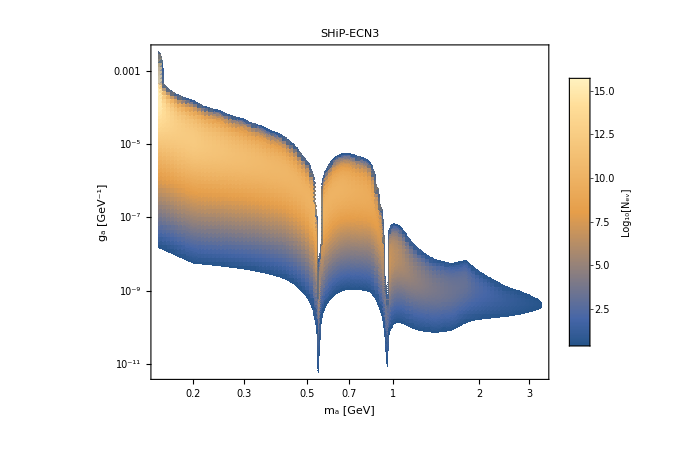

```mathematica
Nevmax=Max[Table[Max[NeventsTabulatedList[[i]][[All,3]]],{i,1,Length[NeventsTabulatedList],1}]];
plot=DensityPlot[Evaluate[Log10[NevTot[ma,fG]]],{ma,mminmaxOverall[[1]],mminmaxOverall[[2]]},{fG,gaminmaxoverall[[1]],gaminmaxoverall[[2]]},ScalingFunctions->{"Log","Log"},AspectRatio->0.78,PlotRange->{All,All,{Log10[2.3],Log10[Nevmax]}},ImageSize->Large,FrameLabel->{"m_a [GeV]","g_a [GeV^-1]" }, Frame-> True, FrameStyle->Directive[Black, 25],PlotPoints->100,PlotLegends->Placed[BarLegend[{Automatic,{Log10[2.3],Log10[Nevmax]}},LegendMarkerSize->340,LegendLabel->Placed["Log_10[N_ev]",Bottom],LabelStyle->{FontSize->22},Method->{FrameStyle->Black,AxesStyle->None,TicksStyle->Black}],Right],PlotLabel->Style[Row[{ExperimentFolder}],20,Black](*,FrameTicks->{{Automatic,Automatic},{TicksPlotx,None}}*)]
(*Export[FileNameJoin[{NotebookDirectory[],"NeventsDensityPlotExample.pdf"}],plot]*)
```

## Sensitivity computation

## Data importing

```mathematica
CHARMboundsTemp=Import[FileNameJoin[{NotebookDirectory[],"contours/BC11/BC11-CHARM.txt"}],"Table"];
CHARMboundsRegion1Temp=Select[CHARMboundsTemp,#[[1]]<0.56&];
CHARMboundsRegion2Temp=Select[CHARMboundsTemp,#[[1]]>0.56&];
CHARMboundsRegion1=CHARMboundsRegion1Temp[[FindShortestTour[{Log10[#[[1]]],Log10[#[[2]]]/20}&/@CHARMboundsRegion1Temp][[2]]]];
CHARMboundsRegion2=CHARMboundsRegion2Temp[[FindShortestTour[{Log10[#[[1]]],Log10[#[[2]]]/20}&/@CHARMboundsRegion2Temp][[2]]]];
OtherBoundsTemp=Import[FileNameJoin[{NotebookDirectory[],"contours/BC11/BC11-no-CHARM.txt"}],"Table"];
OtherBoundsTemp2=OtherBoundsTemp[[FindShortestTour[{Log10[#[[1]]]*2,Log10[#[[2]]]/20}&/@OtherBoundsTemp][[2]]]];
OtherBoundsTemp3=Join[Select[OtherBoundsTemp2,#[[2]]!=0.0020915589095539078&&#[[1]]!=0.9348687893693828&],{{0.93,0.0015},{0.932,0.0021},{0.9388,0.0033},{0.939,0.0029},{0.94,0.002}}];
OtherBounds=OtherBoundsTemp3[[FindShortestTour[{Log10[#[[1]]]*2,Log10[#[[2]]]/20}&/@OtherBoundsTemp3][[2]]]];
```

## Sensitivity

No

6.×10^20

The minimal number of events N_(events, min) for which the sensitivity will be computed:

2.3

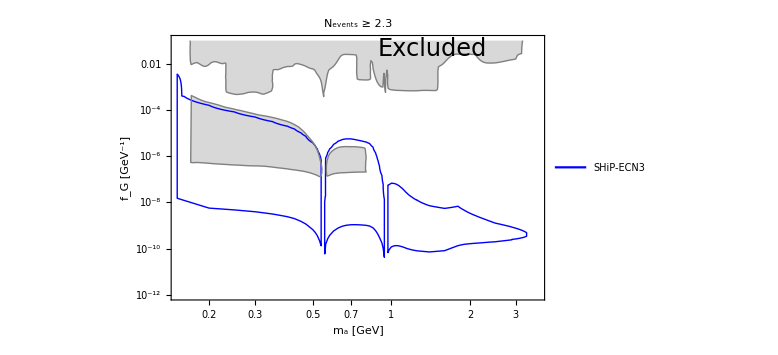

```mathematica
SensitivityBlock[Nev_,Npot_]:=Block[{},
RegSens1=RegionPlot[Npot/NpotDefault NevTot[10^ma,10^ga]*Boole[!(0.538<10^ma<0.555||0.94<10^ma<0.97)]≥Nev,{ma,Log10[mminmaxOverall[[1]]],Log10[0.538]},{ga,Log10[gaminmaxoverall[[1]]],Log10[gaminmaxoverall[[2]]]},PlotPoints->200];
RegSens2=RegionPlot[Npot/NpotDefault NevTot[10^ma,10^ga]*Boole[!(0.538<10^ma<0.555||0.94<10^ma<0.97)]≥Nev,{ma,Log10[0.538],Log10[0.94]},{ga,Log10[gaminmaxoverall[[1]]],Log10[gaminmaxoverall[[2]]]},PlotPoints->200];
RegSens3=RegionPlot[Npot/NpotDefault NevTot[10^ma,10^ga]*Boole[!(0.538<10^ma<0.555||0.94<10^ma<0.97)]≥Nev,{ma,Log10[0.97],Log10[mminmaxOverall[[2]]]},{ga,Log10[gaminmaxoverall[[1]]],Log10[gaminmaxoverall[[2]]]},PlotPoints->200];
(*Sens={10^#[[1]],10^#[[2]]}&/@Partition[Flatten[Cases[Normal@RegSens,Line[x_]:>x,Infinity]],2];*)
SensTemp=Cases[Normal@#,Line[x_]:>x,Infinity]&/@{RegSens1,RegSens2,RegSens3};
SensTemp1=Join[SensTemp[[1]],SensTemp[[2]],SensTemp[[3]]];
Sens=Table[{10^#[[1]],10^#[[2]]}&/@SensTemp1[[i]],{i,1,Length[SensTemp1],1}];
Export[FileNameJoin[{NotebookDirectory[],"Sensitivity domains","ALPs with gluon coupling",ExperimentFolder,ToString@StringForm["Sensitivity_ALP-gluon_at_``_Nev=``_Npot=``.xls",Sequence@@{ExperimentFolder,Nev//ToString,Npot//CForm//ToString}]}],Sens];
Sens
]
choiceNPoT=dropdownDialog[{"Yes","No"},Row[{"The number of proton collisions is ", NpotDefault,". Would you like to change it?"}]]
If[choiceNPoT=="Yes",NpotGivenExperiment=DialogInput[{br=""},Column[{"Enter the number of proton collisions",InputField[Dynamic[br],String],Button["Proceed",DialogReturn[br],ImageSize->Automatic]}]]//ToExpression//N,NpotGivenExperiment=NpotDefault]
Print["The minimal number of events N_(events, min) for which the sensitivity will be computed:"]
NevMinVal=DialogInput[{nev=""},Column[{"Enter the value of N_(events, min) for which the sensitivity will be computed:",InputField[Dynamic[nev],Number],Button["Proceed",DialogReturn[nev],ImageSize->Automatic]}]]//N
sens=SensitivityBlock[NevMinVal,NpotGivenExperiment];
Show[ListLogLogPlot[Cases[{sens,CHARMboundsRegion1,CHARMboundsRegion2,OtherBounds},_?MatrixQ,All],Joined->{True,True,True,True},Frame-> True,FrameLabel->{"m_a [GeV]" , "f_G [GeV^-1]"},FrameStyle->Directive[Black, 23],PlotStyle->Flatten[{ConstantArray[{Thick,Blue},If[MatrixQ[sens],1,Length@sens]],ConstantArray[{Thick,Gray},3]},1],Filling->{Length[sens]+1->{True,Directive[Gray,Opacity[0.3]]},Length[sens]+2->{True,Directive[Gray,Opacity[0.3]]},Length[sens]+3->{True,Directive[Gray,Opacity[0.3]]}},ImageSize->Large,PlotRange->{{1.01mminmaxOverall[[1]],1.1mminmaxOverall[[2]]},{gaminmaxoverall[[1]],0.99gaminmaxoverall[[2]]}},PlotLabel->Style[Row[{"N_events ≥ ",NevMinVal}],18,Black],PlotLegends->Placed[Style[#,15]&/@{GivenExperimentForSensitivityComputation},{0.2,0.15}]](*,LogLogPlot[{x,x^2,x^3,x^4,x^5,x^6},{x,0.05,62.49},PlotStyle->{{Thickness[0.006],Blue},{Thickness[0.006],Darker@Red},{Thickness[0.006],Darker@Red,Dashing[0.02]},{Thickness[0.006],Black},{Thickness[0.01],Darker@Cyan,Dashing[0.007]},{Thick,Darker@Darker@Green,Dashing[0.02]},{Thick,Darker@Red}},PlotLegends->Placed[Style[#,15]&/@{"SHiP","SHADOWS_(specified in LoI)","SHADOWS_(specified by Gaia)", "SHADOWS_(collab estimate)"},{0.26,0.15}]]*),Graphics[{Text[Style["Excluded",24,Black],Scaled[{0.7,0.95}]]}]]
```